## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "windows";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\FKO";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames[[i]]]]

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

#### variables

```mathematica
begin=350;end=14898;average=0.03;
```

Manipulate[ListPlot[data[n], PlotRange -> {0.95, 1.05}], {n, 0, 22, 1}]

#### Samples

Reflexion GK 300-8000

```mathematica
rgk=Table[ListPlot[data[n],PlotStyle->Blue],{n,7,10,1}];
```

Reflexion TQ 1000-15000

```mathematica
rtq=Table[ListPlot[data[n],PlotStyle->Red],{n,15,18,1}];
```

Transmission GK 300-8000

```mathematica
tgk=Table[ListPlot[data[n],PlotStyle->Darker[Blue]],{n,11,14,1}];
```

Reflexion TQ 1000-15000

```mathematica
ttq=Table[ListPlot[data[n],PlotStyle->Darker[Red]],{n,19,22,1}];
```

```mathematica
Manipulate[Show[{rgk⟦im⟧,rtq⟦im⟧}],{im,1,4,1},{e,0.1,10}]
```

```mathematica
ExponentialMovingAverage
```

ExponentialMovingAverage

```mathematica
fctab=Table[Interpolation[ExponentialMovingAverage[data[n],average],InterpolationOrder->1],{n,1,Length[fnames]-1}];
```

```mathematica
fct[n_,cut_,x_:x]:=Piecewise[{{fctab⟦n⟧[x], x<cut}, {fctab⟦n+8⟧[x], x>cut}}]
```

```mathematica
Manipulate[Plot[{fctab⟦n⟧[x],fctab⟦n+8⟧[x],fct[n,cut,x]},{x,500,12000},PlotRange->Full],{n,0,14,1},{cut,1000,10000}]
```

cuts = Table[{n, FindRoot[fctab[[n]][x] - fctab[[n + 8]][x], {x, 4000, 350, 12000}, Compiled -> True]}, {n, 7, 14}];

```mathematica
cuts={{7,4100},{8,3930},{9,3200},{10,2100},{11,3000},{12,2200},{13,4000},{14,3000}}
```

{{7,4100},{8,3930},{9,3200},{10,2100},{11,3000},{12,2200},{13,4000},{14,3000}}

## FP shit

```mathematica
Length[cuts]
```

7

setze reflint = probe 7 (gaas mit cut bei 4100)

```mathematica
reflex[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,1,4}]⟦n-6⟧
```

```mathematica
trans[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,5,8}]⟦n-6⟧
```

```mathematica
Manipulate[Plot[trans[n,x],{x,450,12000}],{n,7,10,1}]
```

```mathematica
d=470*10^-4;
```

```mathematica
Δrg1=0.0;Δrg2=0.0;
```

```mathematica
(*Reflexion einer idealen Grenzfläche in Abhängigkeit von n und κ*)
rg=((n-1)^2+κ^2)/((n+1)^2+κ^2);
```

```mathematica
(*Absorptionskoeffizient*)
β[ν_]:=4*π*Abs[κ]*ν;
```

```mathematica
transth[ν_]:= ((1-rg)(1-rg)*Exp[-β[ν]*d])/(1-(rg)*(rg)*Exp[-2*β[ν]*d]); 
reflth[ν_]:= rg+(((1-(rg))^2)* (rg)*Exp[-2*β[ν]*d])/(1-(rg)*(rg)*Exp[-2*β[ν]*d]);
```

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol=Table[{ν,FindRoot[{transth[ν]-trans[7,ν],reflth[ν]-reflex[7,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,450,14000,4}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsemi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsemi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsemi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]
```

```mathematica
d=440*10^-4;
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν]-trans[8,ν],reflth[ν]-reflex[8,ν]},{n,1.1},{κ,0.0},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,500,12000,6}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlndot=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientndot=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientndot=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]
```

### Functions

```mathematica
brechzahlFCTsemi=Interpolation[ExponentialMovingAverage[brechzahlsemi,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTsemi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
brechzahlFCTndot=Interpolation[ExponentialMovingAverage[brechzahlndot,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTndot=Interpolation[ExponentialMovingAverage[extinktionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
plots={brechzahlFCTsemi,extinktionFCTsemi,brechzahlFCTndot,extinktionFCTndot};
```

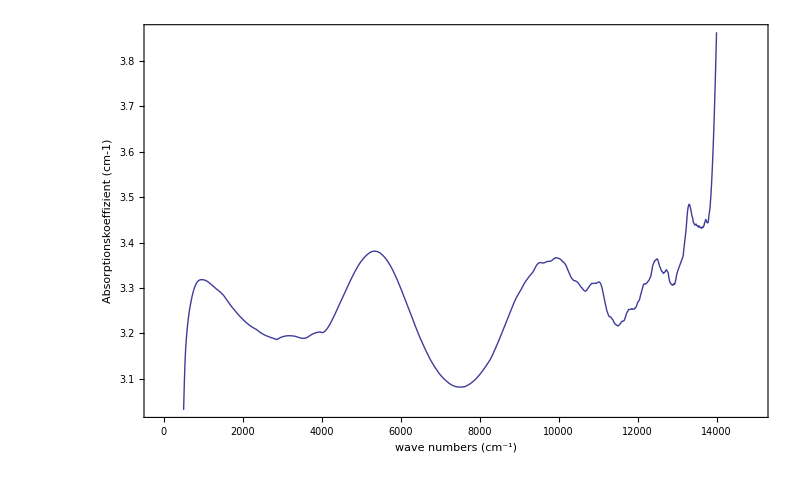
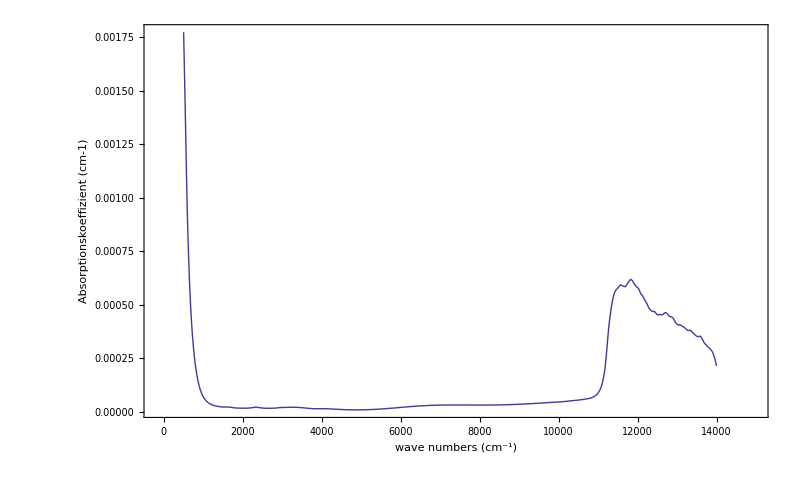
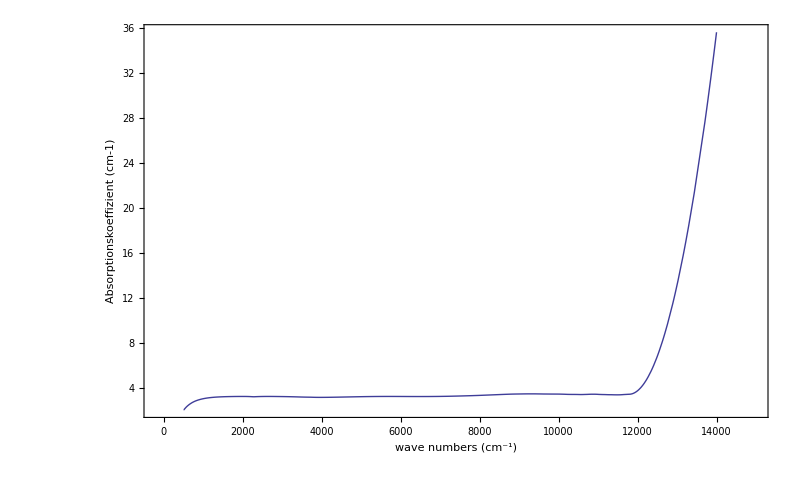
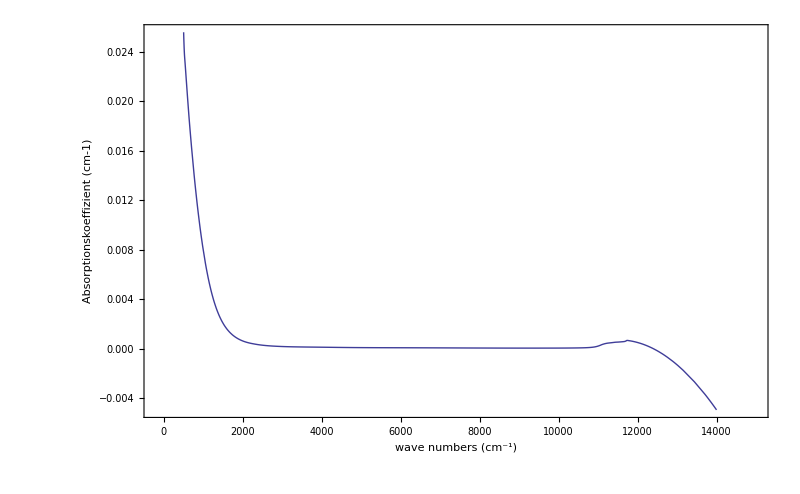

```mathematica
Table[Plot[plots⟦i⟧[x],{x,500,14000},PlotRange->{{-200,15000},Full},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotStyle->Thick,ImageSize->800],{i,1,4}]
```